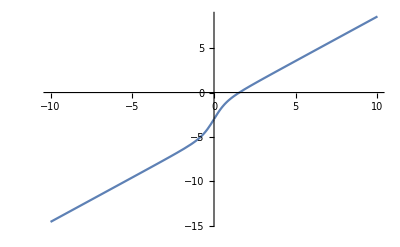

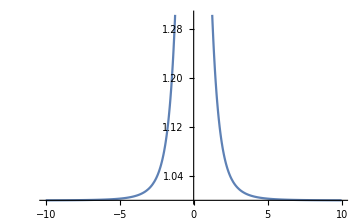

1.

3.

0.666667

1/10000

0

26

1.54712

{1.01674,{x→-3.16064}}

{5.,{x→-9.82326×10^-9}}

2.01674

6.

```mathematica
(*Функция уравнения g(x) = 0*)g[x_]:= x+ ArcTan[x]+x/(1+x^2)-3
dg[x_] := D[g[x], x]
Plot[g[x], {x,-10,10}]
Plot[Evaluate[dg[x]], {x,-10,10}]
(*Ограничитель снизу*)k1 = NMinValue[Abs[dg[x]], x]
(**)k2 = NMaxValue[Abs[dg[x]],x] 
(*Функция итерационного процесса*)target[x_]:=x-1/k2 g[x]
(*Скорость сходимости*)alpha=1-k1/k2
(*а-ка эпсилон*)precision = 10^-4
(*Начальное приближение*)x0 = 0
(*Формула n для погрешности < эпсилон*)n=Floor[1/Log2[alpha] Log2[precision*(1-alpha)/Abs[1/k2 g[x0]]]]+1
intermediateResults=NestList[target,N[x0],n];
res =FixedPoint[target,Last[intermediateResults]]
```